Dianne Hansford

# B - spline curves in MM

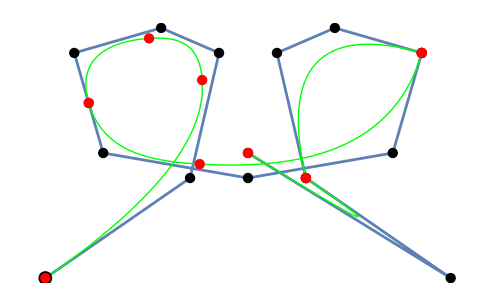

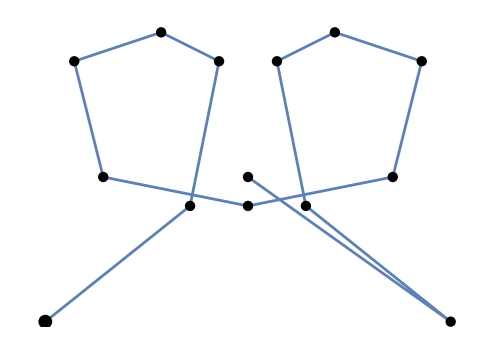

degree = 3  Number segments  = 10

knots = {0.,0.,0.,0.,0.1,0.2,0.3,0.3,0.4,0.6,0.6,0.6,0.9,0.9,0.9,1.,1.,1.,1.}

junction knots = {0.,0.1,0.2,0.3,0.3,0.4,0.6,0.6,0.6,0.9,0.9,0.9,1.}

First deboor point larger

deboor points =(-0.7 | -0.5
-0.2 | -0.1
-0.1 | 0.4
-0.3 | 0.5
-0.6 | 0.4
-0.5 | 0.
0. | -0.1
0.5 | 0.
0.6 | 0.4
0.3 | 0.5
0.1 | 0.4
0.2 | -0.1
0.7 | -0.5
0. | 0.)

```mathematica
(* pick a data set *)
dataset = 1;

If[dataset == 1,(
n=3;  (* degree *)
ll=10;  (* domain intervals *)
numd = n+ll-1+1;
dd={{-0.7,-0.5},
{-0.2,-0.1},
{-0.1,0.4},
{-0.3,0.5},
{-0.6,0.4},
{-0.5,0.0},
{0.0,-0.1},
{0.5,0.0},
{0.6,0.4},
{0.3,0.5},
{0.1,0.4},
{0.2,-0.1},
{0.7,-0.5},
{0.0,0.0}
})];

If[dataset == 2,(
n=3;  (* degree *)
ll=4;  (* domain intervals *)
numd = n+ll-1;
dd = Table[{Cos[x]//N, Sin[x]//N},{x,0,numd}])];

(* Linear *)
If[dataset == 3,(
n=3;  (* degree *)
ll=1;  (* domain intervals *)
numd = n+ll-1;
dd = Table[{x, 0},{x,0,numd}])];

(* data set for example *)
If[dataset == 4,(
n=3;  (* degree *)
ll=7;  (* domain intervals *)
numd = n+ll-1;
dd = Table[{x, 0},{x,0,numd}];
v = 1.0;
dd[[2,2]] =v;
dd[[3,2]] = v;
dd[[6,2]] = v;
dd[[7,2]] = v;
dd[[10,2]] = v
)];

(* data set for example -- not for demo here *)
If[dataset == 5,(
n=3;  (* degree *)
ll=2;  (* domain intervals *)
numd = n+ll-1;
dd = Table[{x, 0},{x,0,numd}];
v = 2.0;
dd[[2,2]] =v;
dd[[3,2]] = v;
dd[[3,1]] = dd[[4,1]] ;
dd[[5,1]] = 10; 
)];



(* uniform knots *)
knot=Join[Table[0,{i,0,n}],{0.1,0.2,0.3,0.3,0.4,0.6,0.6,0.6,0.9,0.9},{1,1,1,1}]//N;
numk = Length[knot];

(* Extract the juntion points *)
(* Evaluate at the domain knots *)
jknots = Table[knot[[i]], {i,n+1,numk - n,1}];
jpts = Table[curve[knot[[i]]], {i,n+1,numk - n,1}];


(* curve evaluation *)
curve[t_]:=Sum[BSplineBasis[{n,knot},i,t]*dd[[i+1]],{i,0,numd}];

(* Plot *)
cplot=ParametricPlot[curve[t],{t,knot[[n+1]],knot[[numk-n]]},PlotStyle->{Thick,Green}];
points=Graphics[{Black,PointSize[0.015],Point[dd],PointSize[0.02],Point[dd[[1]]]}];
ddplot=ListLinePlot[dd];
jptsplot = Graphics[{Red,PointSize[0.015],Point[jpts]}];
Show[{ddplot, cplot,points,jptsplot},Axes-> False]
Show[{ddplot, points}, AspectRatio->Automatic,Axes-> False, PlotRange->All]

Print["degree = ",n,"  Number segments  = ",ll];
Print["knots = ",knot];
Print["junction knots = ",jknots];
Print["First deboor point larger"];
Print["deboor points =",MatrixForm[dd]];
```

#### Move a knot

```mathematica
eps = 0.00001;
imid = Round[numk/2.0];
startval = knot[[imid]];
minv = knot[[imid -1]] + eps ;
maxv = knot[[imid + 1]] - eps;

Print["knots: ",knot];
Print["manipulate knot imid = ",imid];
Print["start value  =",startval];
Print["move between  minv=",minv,"  maxv=",maxv];

Manipulate[(
knot[[imid]] = knotval;
jpts = Table[curve[knot[[i]]], {i,n+1,numk - n,1}];
cplot=ParametricPlot[curve[t],{t,knot[[n+1]],knot[[numk-n]]},PlotStyle->{Thick,Green}];
points=Graphics[{Black,PointSize[0.015],Point[dd],PointSize[0.02],Point[dd[[1]]]}];
ddplot=ListLinePlot[dd];
jptsplot = Graphics[{Red,PointSize[0.015],Point[jpts],Magenta,Point[jpts[[imid-n]]]}];
Show[{ddplot, cplot,points,jptsplot},Axes-> False]), {{knotval,startval},minv,maxv}]
```

knots: {0.,0.,0.,0.,0.1,0.2,0.3,0.3,0.4,0.6,0.6,0.6,0.9,0.9,0.9,1.,1.,1.,1.}

manipulate knot imid = 10

start value  =0.6

move between  minv=0.40001  maxv=0.59999

## Move a control point

```mathematica
ddt = Transpose[dd];

maxmove = Max[ddt[[2]]];
imiddd = Round[numd/2.0];
startdd = dd[[imiddd,2]];
minddy =dd[[imiddd ,2]] - maxmove ;
maxddy = dd[[imiddd ,2]] + maxmove;

Print["manipulate deboor imid = ",imiddd];
Print["start value  =",startdd];
Print["move between  minddy=",minddy,"  maxddy=",maxddy];

vminx = Min[ddt[[1]]];
vmaxx = Max[ddt[[1]]];
vminy = Min[ddt[[2]]];
vmaxy = Max[ddt[[2]]] + maxmove;
Print["control polygon min and max ",vminx," ",vmaxx,"  ",vminy,"  ",vmaxy];


 
Manipulate[(
dd[[imiddd,2]] = ddval;
jpts = Table[curve[knot[[i]]], {i,n+1,numk - n,1}];
cplot=ParametricPlot[curve[t],{t,knot[[n+1]],knot[[numk-n]]},PlotStyle->{Thick,Green}];
points=Graphics[{Black,PointSize[0.015],Point[dd],PointSize[0.02],Point[dd[[1]]]}];
ddplot=ListLinePlot[dd];
jptsplot = Graphics[{Red,PointSize[0.015],Point[jpts],Magenta,Point[jpts[[imid-n]]]}];
Show[{ddplot, cplot,points,jptsplot},Axes-> False,PlotRange->{{vminx,vmaxx},{vminy,vmaxy}}]),
 {{ddval,startdd},minddy,maxddy}]
```

manipulate deboor imid = 6

start value  =0.

move between  minddy=-0.5  maxddy=0.5

control polygon min and max -0.7 0.7  -0.5  1.

Derivative of the curve

```mathematica
curve'[0.5]
```

{4.125,1.91667}